### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =5;
d = 1;
lm = 1;
lp[k_]:=((k+1)^-(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

### Evaluating the normalization

```mathematica
efun[x_,y_,a_,b_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x^2+y^2)] Exp[b^2(Np-1)/(a-b(Np-1)) x y];
efunpoly[x_,y_,a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x^2+y^2) +(b^2(Np-1)/(a-b(Np-1)) x y)(*normalization includes combinatorial factor of 5 since we are considering 1parRDO in 5 particle system*) 
normPre[a_,b_]:=5*((5 π)/(√2 √((a (a-5 b))/(a-4 b))))^(-1);

(*here we have defined the Spin Up and Spin Down contributions of the 1par RDO polynomial from a groundstate with two spin downs and one spin up*)
FpolySpinUp[x1_,y1_,a_,b_]:=1/(a-4 b)^2 √π (12 b^2+4 a^3 x1 y1+a b (-7+b (9 x1+y1) (x1+9 y1))+a^2 (1-2 b (x1^2+18 x1 y1+y1^2)));
FpolySpinDown[x1_,y1_,a_,b_]:=1/(2 (a-4 b)^4)√π (816 b^4+16 a^6 x1^2 y1^2-4 a^5 (x1^2-2 x1 y1+4 b x1^3 y1+y1^2+72 b x1^2 y1^2+4 b x1 y1^3)-4 a^3 b (12+b^2 (9 x1+y1) (x1+9 y1) (x1^2+18 x1 y1+y1^2)+3 b (37 x1^2-46 x1 y1+37 y1^2))-8 a b^3 (99+b (187 x1^2-74 x1 y1+187 y1^2))+a^2 b^2 (291+b^2 (9 x1+y1)^2 (x1+9 y1)^2+2 b (659 x1^2-538 x1 y1+659 y1^2))+a^4 (3+4 b (17 x1^2-28 x1 y1+17 y1^2)+4 b^2 (x1^4+54 x1^3 y1+490 x1^2 y1^2+54 x1 y1^3+y1^4)));
```

```mathematica
rho1uu[a_,b_]:=normPre[a,b]*FpolySpinUp[x1,x1p,a,b]
rho1dd[a_,b_] := normPre[a,b]*FpolySpinDown[x1,x1p,a,b]
```

```mathematica
(*define 2 particle hf basis*)
(*modes are always defined such that for multi spin basis mode1 = UP and mode2 = DOWN*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 2 - RDO

```mathematica
(*Determine the coefficients of the polynomial 'polystart' which is a product of hermite polynomials and the 1parRDO, by the coefficientlist function where q corresponds to the power i.e. x^q and importantly not to the index in the Mathematica native CoefficientList function  *)
```

```mathematica
polystartd[mode1_]:=hfcoef[mode1,x1, a]*hfcoef[mode1,x1p, a]*rho1dd[a,b]
```

```mathematica
polystartu[mode1_]:=hfcoef[mode1,x1, a]*hfcoef[mode1,x1p, a]*rho1uu[a,b]
```

```mathematica
coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*perform sanity check to see whether the coefficient decomposition has been performed correctly*)
```

```mathematica
Sum[coefstart[polystartd[5],x1,q]*x1^q,{q,0,maxdegreestart[polystartd[5],x1]}]-polystartd[5]//Simplify
```

0

### Defining exponential

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
(*exppolyinit describes the exponential contribution of the 1 particle RDO*)
```

```mathematica
exppolyinit=efunpoly[x1,x1p,a,b]-a(x1^2+x1p^2);
```

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
(*sanity check*)
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

### Performing algorithm to integrate 2-par RDO

```mathematica
(* the intxmab function is the results of the following integral:
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*, it gives the integral over all space of x^m* Exp[a x^2+b x], where the function inputs correspond to the polynomial power, quadratic and linear exponential coefficient respectively *)
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
(*inxmabpoly returns the polynomial contribution of the integration inxmab*)
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
(*intexppoly defines the remaining part of the exponential function which in "Running the algorithm" consists of all the coefficients in the remaining variables*)
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
(*int1poly is the initial polynomial used to run the integration algorithm which iteratively applies the intmxab function to all different variables one after the other. x1 has been picked as the first integration variable, intgenpoly takes a subsequently evaluated polynomial poly as input to evaluate the integral with respect to the exppoly expontial and the variable xint*)
```

```mathematica
int1poly[m1_, s1_]:= Sum[If[s1==-1, coefstart[polystartd[m1],x1, q ],  coefstart[polystartu[m1],x1, q ]]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[If[s1==-1, polystartd[m1], polystartu[m1]],x1]}]
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

### Running the algorithm

```mathematica
(*the algorithm runs recursively,such that polyi and exppolyi where i=(1,2) define the relevant polynomials and exponential functions which arise from integrating in the various variables*)
```

```mathematica
(*mode and its spin are specified below, we only calculate expectation values which are diagonal in the mode-reduced density operator so the modes of the primed and unprimed coordinates are always the same here*)
mode1 =1;
spin1=0;
```

```mathematica
poly1 = int1poly[mode1, spin1];
```

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify;
```

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x1p] // Simplify;
```

```mathematica
exppoly2 = efuncoef[exppoly1, x1p, 0] + intexppoly[efuncoef[exppoly1, x1p, 2], efuncoef[exppoly1, x1p, 1]] // Simplify;
```

```mathematica
finalanswer = poly2*Exp[exppoly2] // Simplify
```

(√a √((a (a-5 b))/(a-4 b)) b^8 (8637440 a^10-215936000 a^9 b+2512321280 a^8 b^2-17856025600 a^7 b^3+84049420672 a^6 b^4-265171070080 a^5 b^5+545165914848 a^4 b^6-674883228480 a^3 b^7+416536368540 a^2 b^8-73561286700 a b^9+18714751479 b^10))/(64 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^9 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))

```mathematica
p0dint[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) (32 a^4-320 a^3 b+980 a^2 b^2-900 a b^3+291 b^4))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^2 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p0dfinal[k_,Np_]:=p0dint[A[lp[k]], B[1,lp[k], Np]]
```

```mathematica
p0dfinal[0,5]
```

1

```mathematica
p33int[a_,b_]:=1/(65536 a (a-2 b)^8 (a-b)^(15/2))5 √(a-3 b) b^6 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (5120 a^8-61440 a^7 b+312960 a^6 b^2-881280 a^5 b^3+1508784 a^4 b^4-1639584 a^3 b^5+1159216 a^2 b^6-531840 a b^7+131067 b^8)
p33final[k_]:=p33int[A[lp[k]], B[1,lp[k],Np]]
```

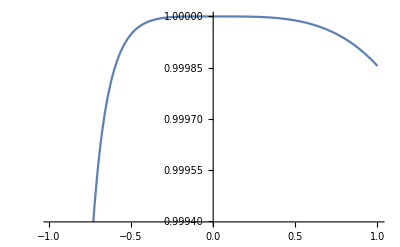

```mathematica
Plot[p0dfinal[k,3], {k,-0.99,1}]
```

```mathematica
(*intbos2rdofull[m1,m2,n1,n2]:=
Module[{poly, exppoly},
poly1[1] = int1poly[mode1, mode2, mode3, mode4] // Simplify;
	exppoly[1] = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify;
poly[2] = intgenpoly[poly[1], exppoly[1], x2];
exppoly[2] = efuncoef[exppoly[1], x2, 0] + intexppoly[efuncoef[exppoly[1], x2, 2], efuncoef[exppoly[1], x2, 1]] // Simplify;
poly[3] = intgenpoly[poly[2], exppoly[2], x1p] // Simplify;
exppoly[3] = efuncoef[exppoly[2], x1p, 0] + intexppoly[efuncoef[exppoly[2], x1p, 2], efuncoef[exppoly[2], x1p, 1]] // Simplify;
poly[4] = intgenpoly[poly[3], exppoly[3], x2p] // Simplify;
exppoly[4] = efuncoef[exppoly[3], x2p, 0] + intexppoly[efuncoef[exppoly[3], x2p, 2], efuncoef[exppoly[3], x2p, 1]] //Simplify;
poly[4]
]*)
```